```mathematica
R0=({{2/3, -1/3, -2/3}, {-1/3, 2/3, -2/3}, {2/3, 2/3, 1/3}});R1=({{2/3, 2/3, 1/3}, {-2/3, 1/3, 2/3}, {1/3, -2/3, 2/3}});R2=({{1/3, -2/3, 2/3}, {2/3, 2/3, 1/3}, {-2/3, 1/3, 2/3}});R3=({{1/3, -2/3, 2/3}, {-2/3, -2/3, -1/3}, {2/3, -1/3, -2/3}});
```

```mathematica
D0=({{2/(√6), (1-ⅈ)/(√6)}, {(-1-ⅈ)/(√6), 2/(√6)}});D1=({{(-2-ⅈ)/(√6), -ⅈ/(√6)}, {-ⅈ/(√6), (-2+ⅈ)/(√6)}});D2=({{(2-ⅈ)/(√6), -1/(√6)}, {1/(√6), (2+ⅈ)/(√6)}});D3=({{-ⅈ/(√6), (1-2ⅈ)/(√6)}, {(-1-2ⅈ)/(√6), ⅈ/(√6)}});
```

```mathematica
τ03=-({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});τ30=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});τ02=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});τ20=-({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});τ01=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});τ10=-({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});τ12=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});τ21=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});τ13=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});τ31=-({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});τ23=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});τ32=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});
```

```mathematica
T03=KroneckerProduct[τ03.Transpose[R0].R3.τ30,ConjugateTranspose[D0].D3];
```

```mathematica
T02=KroneckerProduct[τ02.Transpose[R0].R2.τ20,ConjugateTranspose[D0].D2];
```

```mathematica
T01=KroneckerProduct[τ01.Transpose[R0].R1.τ10,ConjugateTranspose[D0].D1];
```

```mathematica
T12=KroneckerProduct[τ12.Transpose[R1].R2.τ21,ConjugateTranspose[D1].D2];
```

```mathematica
T13=KroneckerProduct[τ13.Transpose[R1].R3.τ31,ConjugateTranspose[D1].D3];
```

```mathematica
T23=KroneckerProduct[τ23.Transpose[R2].R3.τ32,ConjugateTranspose[D2].D3];
```

```mathematica
MatrixForm[Cos[b]T01]
```

((-4/9-(4 ⅈ)/27) Cos[b] | (4/27-(20 ⅈ)/27) Cos[b] | (1/18+ⅈ/54) Cos[b] | (-1/54+(5 ⅈ)/54) Cos[b] | 0 | 0
(-4/27-(20 ⅈ)/27) Cos[b] | (-4/9+(4 ⅈ)/27) Cos[b] | (1/54+(5 ⅈ)/54) Cos[b] | (1/18-ⅈ/54) Cos[b] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
(-1/18-ⅈ/54) Cos[b] | (1/54-(5 ⅈ)/54) Cos[b] | (4/9+(4 ⅈ)/27) Cos[b] | (-4/27+(20 ⅈ)/27) Cos[b] | 0 | 0
(-1/54-(5 ⅈ)/54) Cos[b] | (-1/18+ⅈ/54) Cos[b] | (4/27+(20 ⅈ)/27) Cos[b] | (4/9-(4 ⅈ)/27) Cos[b] | 0 | 0)

```mathematica
MatrixForm[Cos[c]T02]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
(-1/18+ⅈ/54) Cos[c] | (5/54-ⅈ/54) Cos[c] | (4/9-(4 ⅈ)/27) Cos[c] | (-20/27+(4 ⅈ)/27) Cos[c] | 0 | 0
(-5/54-ⅈ/54) Cos[c] | (-1/18-ⅈ/54) Cos[c] | (20/27+(4 ⅈ)/27) Cos[c] | (4/9+(4 ⅈ)/27) Cos[c] | 0 | 0
(-4/9+(4 ⅈ)/27) Cos[c] | (20/27-(4 ⅈ)/27) Cos[c] | (1/18-ⅈ/54) Cos[c] | (-5/54+ⅈ/54) Cos[c] | 0 | 0
(-20/27-(4 ⅈ)/27) Cos[c] | (-4/9-(4 ⅈ)/27) Cos[c] | (5/54+ⅈ/54) Cos[c] | (1/18+ⅈ/54) Cos[c] | 0 | 0)

```mathematica
MatrixForm[Cos[d]T03]
```

((4/9-(4 ⅈ)/27) Cos[d] | (4/27-(20 ⅈ)/27) Cos[d] | 0 | 0 | (1/18-ⅈ/54) Cos[d] | (1/54-(5 ⅈ)/54) Cos[d]
(-4/27-(20 ⅈ)/27) Cos[d] | (4/9+(4 ⅈ)/27) Cos[d] | 0 | 0 | (-1/54-(5 ⅈ)/54) Cos[d] | (1/18+ⅈ/54) Cos[d]
(-1/18+ⅈ/54) Cos[d] | (-1/54+(5 ⅈ)/54) Cos[d] | 0 | 0 | (-4/9+(4 ⅈ)/27) Cos[d] | (-4/27+(20 ⅈ)/27) Cos[d]
(1/54+(5 ⅈ)/54) Cos[d] | (-1/18-ⅈ/54) Cos[d] | 0 | 0 | (4/27+(20 ⅈ)/27) Cos[d] | (-4/9-(4 ⅈ)/27) Cos[d]
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[Cos[c-b]T12]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
(-4/9+(20 ⅈ)/27) Cos[b-c] | (4/27+(4 ⅈ)/27) Cos[b-c] | 0 | 0 | (-1/18+(5 ⅈ)/54) Cos[b-c] | (1/54+ⅈ/54) Cos[b-c]
(-4/27+(4 ⅈ)/27) Cos[b-c] | (-4/9-(20 ⅈ)/27) Cos[b-c] | 0 | 0 | (-1/54+ⅈ/54) Cos[b-c] | (-1/18-(5 ⅈ)/54) Cos[b-c]
(-1/18+(5 ⅈ)/54) Cos[b-c] | (1/54+ⅈ/54) Cos[b-c] | 0 | 0 | (-4/9+(20 ⅈ)/27) Cos[b-c] | (4/27+(4 ⅈ)/27) Cos[b-c]
(-1/54+ⅈ/54) Cos[b-c] | (-1/18-(5 ⅈ)/54) Cos[b-c] | 0 | 0 | (-4/27+(4 ⅈ)/27) Cos[b-c] | (-4/9-(20 ⅈ)/27) Cos[b-c])

```mathematica
MatrixForm[Cos[d-b]T13]
```

((4/9+(4 ⅈ)/27) Cos[b-d] | (-4/27+(20 ⅈ)/27) Cos[b-d] | (-1/18-ⅈ/54) Cos[b-d] | (1/54-(5 ⅈ)/54) Cos[b-d] | 0 | 0
(4/27+(20 ⅈ)/27) Cos[b-d] | (4/9-(4 ⅈ)/27) Cos[b-d] | (-1/54-(5 ⅈ)/54) Cos[b-d] | (-1/18+ⅈ/54) Cos[b-d] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
(1/18+ⅈ/54) Cos[b-d] | (-1/54+(5 ⅈ)/54) Cos[b-d] | (-4/9-(4 ⅈ)/27) Cos[b-d] | (4/27-(20 ⅈ)/27) Cos[b-d] | 0 | 0
(1/54+(5 ⅈ)/54) Cos[b-d] | (1/18-ⅈ/54) Cos[b-d] | (-4/27-(20 ⅈ)/27) Cos[b-d] | (-4/9+(4 ⅈ)/27) Cos[b-d] | 0 | 0)

```mathematica
MatrixForm[Cos[d-c]T23]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2/27 ⅈ Cos[c-d] | (-2/27+ⅈ/27) Cos[c-d] | 16/27 ⅈ Cos[c-d] | (-16/27+(8 ⅈ)/27) Cos[c-d]
0 | 0 | (2/27+ⅈ/27) Cos[c-d] | -2/27 ⅈ Cos[c-d] | (16/27+(8 ⅈ)/27) Cos[c-d] | -16/27 ⅈ Cos[c-d]
0 | 0 | 16/27 ⅈ Cos[c-d] | (-16/27+(8 ⅈ)/27) Cos[c-d] | 2/27 ⅈ Cos[c-d] | (-2/27+ⅈ/27) Cos[c-d]
0 | 0 | (16/27+(8 ⅈ)/27) Cos[c-d] | -16/27 ⅈ Cos[c-d] | (2/27+ⅈ/27) Cos[c-d] | -2/27 ⅈ Cos[c-d])

```mathematica
MatrixForm[Table[0,{i,6},{j,2}]]
```

```mathematica
p=1/Sqrt[3]({{-1, 0}, {0, 1}, {I, 0}, {0, I}, {0, 1}, {1, 0}})
```

{{-1/(√3),0},{0,1/(√3)},{ⅈ/(√3),0},{0,ⅈ/(√3)},{0,1/(√3)},{1/(√3),0}}

```mathematica
MatrixForm[p]
```

(-1/(√3) | 0
0 | 1/(√3)
ⅈ/(√3) | 0
0 | ⅈ/(√3)
0 | 1/(√3)
1/(√3) | 0)

```mathematica
MatrixForm[ConjugateTranspose[p]]
```

(-1/(√3) | 0 | -ⅈ/(√3) | 0 | 0 | 1/(√3)
0 | 1/(√3) | 0 | -ⅈ/(√3) | 1/(√3) | 0)

```mathematica
MatrixForm[Cos[b]ConjugateTranspose[p].T01.p]
```

((-31/81+ⅈ/81) Cos[b] | (1/81+(11 ⅈ)/27) Cos[b]
(-1/81+(11 ⅈ)/27) Cos[b] | (-31/81-ⅈ/81) Cos[b])

```mathematica
MatrixForm[Cos[c]ConjugateTranspose[p].T02.p]
```

((31/81+ⅈ/81) Cos[c] | (-11/27-ⅈ/81) Cos[c]
(11/27-ⅈ/81) Cos[c] | (31/81-ⅈ/81) Cos[c])

```mathematica
MatrixForm[Cos[d]ConjugateTranspose[p].T03.p]
```

((31/81+ⅈ/81) Cos[d] | (1/81+(11 ⅈ)/27) Cos[d]
(-1/81+(11 ⅈ)/27) Cos[d] | (31/81-ⅈ/81) Cos[d])

```mathematica
MatrixForm[Cos[c-b]ConjugateTranspose[p].T12.p]
```

((-31/81-(11 ⅈ)/27) Cos[b-c] | (1/81-ⅈ/81) Cos[b-c]
(-1/81-ⅈ/81) Cos[b-c] | (-31/81+(11 ⅈ)/27) Cos[b-c])

```mathematica
MatrixForm[Cos[d-b]ConjugateTranspose[p].T13.p]
```

((31/81-ⅈ/81) Cos[b-d] | (-1/81-(11 ⅈ)/27) Cos[b-d]
(1/81-(11 ⅈ)/27) Cos[b-d] | (31/81+ⅈ/81) Cos[b-d])

```mathematica
MatrixForm[Cos[d-c]ConjugateTranspose[p].T23.p]
```

(32/81 ⅈ Cos[c-d] | (32/81+(2 ⅈ)/81) Cos[c-d]
(-32/81+(2 ⅈ)/81) Cos[c-d] | -32/81 ⅈ Cos[c-d])

```mathematica
MatrixForm[KroneckerProduct[Table[Abs[i-j],{i,4},{j,4}],Table[1,{i,2},{j,2}]]]
```

```mathematica
Half=({{0, 0, (-31/81+ⅈ/81) Cos[b], (1/81+(11 ⅈ)/27) Cos[b], (31/81+ⅈ/81) Cos[c], (-11/27-ⅈ/81) Cos[c], (31/81+ⅈ/81) Cos[d], (1/81+(11 ⅈ)/27) Cos[d]}, {0, 0, (-1/81+(11 ⅈ)/27) Cos[b], (-31/81-ⅈ/81) Cos[b], (11/27-ⅈ/81) Cos[c], (31/81-ⅈ/81) Cos[c], (-1/81+(11 ⅈ)/27) Cos[d], (31/81-ⅈ/81) Cos[d]}, {0, 0, 0, 0, (-31/81-(11 ⅈ)/27) Cos[b-c], (1/81-ⅈ/81) Cos[b-c], (31/81-ⅈ/81) Cos[b-d], (-1/81-(11 ⅈ)/27) Cos[b-d]}, {0, 0, 0, 0, (-1/81-ⅈ/81) Cos[b-c], (-31/81+(11 ⅈ)/27) Cos[b-c], (1/81-(11 ⅈ)/27) Cos[b-d], (31/81+ⅈ/81) Cos[b-d]}, {0, 0, 0, 0, 0, 0, 32/81 ⅈ Cos[c-d], (32/81+(2 ⅈ)/81) Cos[c-d]}, {0, 0, 0, 0, 0, 0, (-32/81+(2 ⅈ)/81) Cos[c-d], -32/81 ⅈ Cos[c-d]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
H=Half+ConjugateTranspose[Half];
```

```mathematica
MatrixForm[H]
```

```mathematica
HH[b_,c_,d_]:=({{0, 0, (-31/81+ⅈ/81) Cos[b], (1/81+(11 ⅈ)/27) Cos[b], (31/81+ⅈ/81) Cos[c], (-11/27-ⅈ/81) Cos[c], (31/81+ⅈ/81) Cos[d], (1/81+(11 ⅈ)/27) Cos[d]}, {0, 0, (-1/81+(11 ⅈ)/27) Cos[b], (-31/81-ⅈ/81) Cos[b], (11/27-ⅈ/81) Cos[c], (31/81-ⅈ/81) Cos[c], (-1/81+(11 ⅈ)/27) Cos[d], (31/81-ⅈ/81) Cos[d]}, {(-31/81-ⅈ/81) Conjugate[Cos[b]], (-1/81-(11 ⅈ)/27) Conjugate[Cos[b]], 0, 0, (-31/81-(11 ⅈ)/27) Cos[b-c], (1/81-ⅈ/81) Cos[b-c], (31/81-ⅈ/81) Cos[b-d], (-1/81-(11 ⅈ)/27) Cos[b-d]}, {(1/81-(11 ⅈ)/27) Conjugate[Cos[b]], (-31/81+ⅈ/81) Conjugate[Cos[b]], 0, 0, (-1/81-ⅈ/81) Cos[b-c], (-31/81+(11 ⅈ)/27) Cos[b-c], (1/81-(11 ⅈ)/27) Cos[b-d], (31/81+ⅈ/81) Cos[b-d]}, {(31/81-ⅈ/81) Conjugate[Cos[c]], (11/27+ⅈ/81) Conjugate[Cos[c]], (-31/81+(11 ⅈ)/27) Cos[Conjugate[b]-Conjugate[c]], (-1/81+ⅈ/81) Cos[Conjugate[b]-Conjugate[c]], 0, 0, 32/81 ⅈ Cos[c-d], (32/81+(2 ⅈ)/81) Cos[c-d]}, {(-11/27+ⅈ/81) Conjugate[Cos[c]], (31/81+ⅈ/81) Conjugate[Cos[c]], (1/81+ⅈ/81) Cos[Conjugate[b]-Conjugate[c]], (-31/81-(11 ⅈ)/27) Cos[Conjugate[b]-Conjugate[c]], 0, 0, (-32/81+(2 ⅈ)/81) Cos[c-d], -32/81 ⅈ Cos[c-d]}, {(31/81-ⅈ/81) Conjugate[Cos[d]], (-1/81-(11 ⅈ)/27) Conjugate[Cos[d]], (31/81+ⅈ/81) Cos[Conjugate[b]-Conjugate[d]], (1/81+(11 ⅈ)/27) Cos[Conjugate[b]-Conjugate[d]], -32/81 ⅈ Cos[Conjugate[c]-Conjugate[d]], (-32/81-(2 ⅈ)/81) Cos[Conjugate[c]-Conjugate[d]], 0, 0}, {(1/81-(11 ⅈ)/27) Conjugate[Cos[d]], (31/81+ⅈ/81) Conjugate[Cos[d]], (-1/81+(11 ⅈ)/27) Cos[Conjugate[b]-Conjugate[d]], (31/81-ⅈ/81) Cos[Conjugate[b]-Conjugate[d]], (32/81-(2 ⅈ)/81) Cos[Conjugate[c]-Conjugate[d]], 32/81 ⅈ Cos[Conjugate[c]-Conjugate[d]], 0, 0}})
```

```mathematica
F[b_,c_,d_]:=Sort[Eigenvalues[HH[b,c,d]]]
```

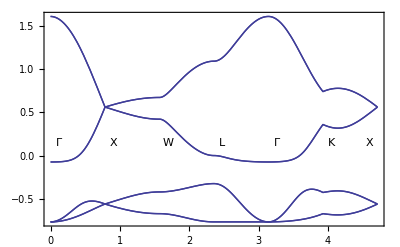

```mathematica
Plot[Piecewise[{{F[2t,0,2t],t≥0&&t<Pi/4},{F[Pi/2,t-Pi/4,t-Pi/4+Pi/2],t≥Pi/4&&t<Pi/2},{F[Pi/2,Pi/4+t-Pi/2,3Pi/4-t+Pi/2],t≥Pi/2&&t<3Pi/4},{F[Pi/2-2(t-3Pi/4),Pi/2-2(t-3Pi/4),Pi/2-2(t-3Pi/4)],t≥3Pi/4&&t<Pi},{F[3/2(t-Pi),3/2(t-Pi),3(t-Pi)],t≥Pi&&t<5Pi/4},{F[3Pi/8+t/2-5Pi/8,3Pi/8-3t/2+15Pi/8,3Pi/4-(t-5Pi/4)],t≥5Pi/4&&t≤3Pi/2}}],{t,0,3Pi/2},GridLines->{{{0,Dashed},{Pi/4,Dashed},{2Pi/4,Dashed},{3Pi/4,Dashed},{Pi,Dashed},{5Pi/4,Dashed},{3Pi/2,Dashed}},{}},Epilog->{Inset["Γ",{0.12,0.15}],Inset["X",{Pi/4+0.12,0.15}],Inset["W",{2Pi/4+0.12,0.15}],Inset["L",{3Pi/4+0.12,0.15}],Inset["Γ",{Pi+0.12,0.15}],Inset["K",{5Pi/4+0.12,0.15}],Inset["X",{6Pi/4-0.12,0.15}]},Frame->True]
```